```mathematica
xvsu[uc_,uh_]:=Module[{xvsutb={},xvsutb2={}},
For[i=0,i<=3,i+=0.01,
uu=uc*10^i;
x=Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,uu}]];
AppendTo[xvsutb,{uu,x}];
];
xvsutb2=Join[Reverse[xvsutb],Transpose[{xvsutb[[All,1]],-xvsutb[[All,2]]}]];
Return[xvsutb2];
]
```

```mathematica
xvsu1010=xvsu[1,1];
xvsu1210=xvsu[1.2,1];
xvsu4010=xvsu[4,1];
```

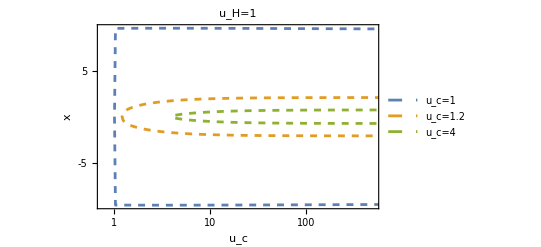

```mathematica
Show[ListLinePlot[{xvsu1010,xvsu1210,xvsu4010},ScalingFunctions->{"Log","SignedLog"},PlotRange->{{0,500},Automatic},Frame->True,FrameLabel->{"u_c","x"},PlotLegends->{"u_c=1","u_c=1.2","u_c=4"},FrameTicks->{{{-40,-10,-5,0,5,10,40},None},{Automatic,None}},PlotStyle->Dashed],RotateLabel->False,PlotLabel->"u_H=1"]
```

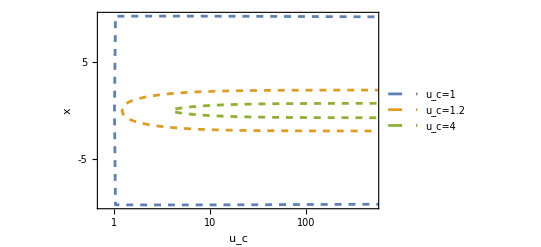

```mathematica
symxplt=ListLinePlot[{xvsu1010,xvsu1210,xvsu4010},ScalingFunctions->{"Log","SignedLog"},PlotRange->{{0,500},Automatic},Frame->True,FrameLabel->{"u_c","x"},PlotLegends->{"u_c=1","u_c=1.2","u_c=4"},FrameTicks->{{{-40,-10,-5,0,5,10,40},None},{Automatic,None}},PlotStyle->Dashed]
```

```mathematica
lvsuc[uh_]:=Module[{lvsuctb={}},
For[i=0,i<=2.5,i+=0.005,uc=2^i-0.93;
l=2*Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,Infinity}]];
If[FreeQ[l,Complex],AppendTo[lvsuctb,{uc,l}]];
];
Return[lvsuctb];
]
```

```mathematica
lvsuc1=lvsuc[1];
lvsuc05=lvsuc[0.5];
lvsuc0=lvsuc[0];
```

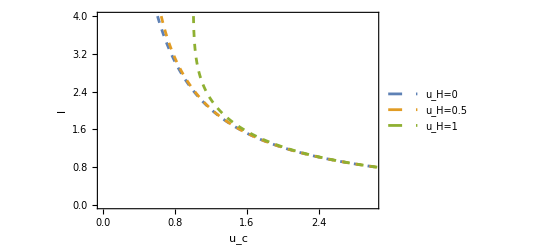

```mathematica
Show[ListLinePlot[{lvsuc0,lvsuc05,lvsuc1},Frame->True,PlotRange->{{0,3},{0,4}},FrameLabel->{"u_c","l"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed],RotateLabel->False]
```

```mathematica
symlplt=ListLinePlot[{lvsuc0,lvsuc05,lvsuc1},Frame->True,PlotRange->{{0,3},{0,4}},FrameLabel->{"u_c","l"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed]
```

-Graphics-

```mathematica
symadiv=Integrate[u/Sqrt[1-(uh/u)^4],{u,uh,ub}]
```

1/2 √(ub^4-uh^4)

```mathematica
Series[symadiv,{ub,Infinity,2}]
```

ub^2/2-uh^4/(4 ub^2)+O[1/ub]^3

```mathematica
symdelsfunc[uh_,ub_]:=Module[{spvsltb={}},
For[uc=uh+0.0000001,uc<=3,uc+=0.025,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
sp=2*(Quiet[NIntegrate[u/Sqrt[(1-(uc/u)^6)(1-(uh/u)^4)],{u,uc,ub}]]-1/2 √(ub^4-uh^4));
AppendTo[spvsltb,{l,sp}];
];
Return[spvsltb];
];
```

```mathematica
symdelsvsl07=symdelsfunc[0,7];
symdelsvsl057=symdelsfunc[0.5,7];
symdelsvsl17=symdelsfunc[1,7];
```

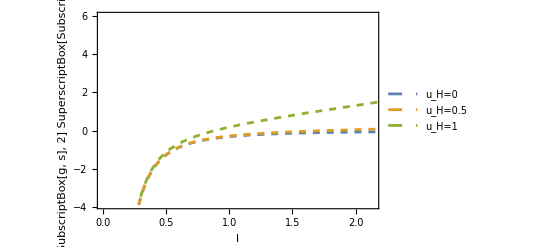

```mathematica
symdelsplt=ListLinePlot[{symdelsvsl07,symdelsvsl057,symdelsvsl17},Frame->True,FrameLabel->{"l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed]
```

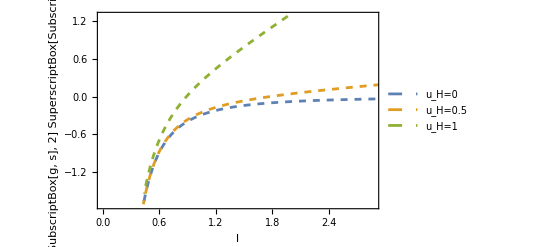

```mathematica
Show[ListLinePlot[{symdelsvsl07,symdelsvsl057,symdelsvsl17},Frame->True,FrameLabel->{"l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"},PlotLegends->{"u_H=0","u_H=0.5","u_H=1"},PlotStyle->Dashed],RotateLabel->False]
```

```mathematica
symucvslinterp[uh_,ub_]:=Module[{ucvsltb={}},
For[uc=uh,uc<=3,uc+=0.01,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
If[FreeQ[l,Complex],AppendTo[ucvsltb,{l,uc}]];
];
Clear[l];
Return[Interpolation[ucvsltb,InterpolationOrder->5]];
];
```

```mathematica
symlinterptest=symucvslinterp[1,7]
```

InterpolatingFunction[…]

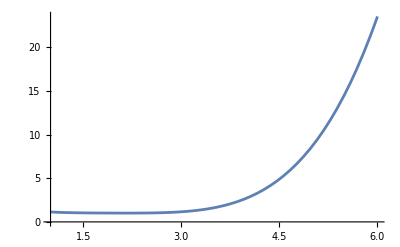

```mathematica
Plot[symlinterptest[l],{l,1,6}]
```

```mathematica
symmutinffuncxl[uh_,ub_,l_]:=Module[{mutinfvsxltb={}},
firstucfunc=symucvslinterp[uh,ub];
ucl=firstucfunc[l];
splint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucl/u)^6)(1-(uh/u)^4)],{u,ucl,ub}]];
For[i=0,i<=1,i+=0.005,
x=i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
spxint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucx/u)^6)(1-(uh/u)^4)],{u,ucx,ub}]];
sp2lxint=2*Quiet[NIntegrate[u/Sqrt[(1-(uc2lx/u)^6)(1-(uh/u)^4)],{u,uc2lx,ub}]];
mutinf=2*splint-sp2lxint-spxint;
If[FreeQ[mutinf,Complex],AppendTo[mutinfvsxltb,{x/l,mutinf}]];
];
Return[mutinfvsxltb];
];
```

```mathematica
symmutinf0201=Quiet[symmutinffuncxl[0,20,1]];
symmutinf01201=Quiet[symmutinffuncxl[0.1,20,1]];
symmutinf015201=Quiet[symmutinffuncxl[0.15,20,1]];
symmutinf02201=Quiet[symmutinffuncxl[0.2,20,1]];
```

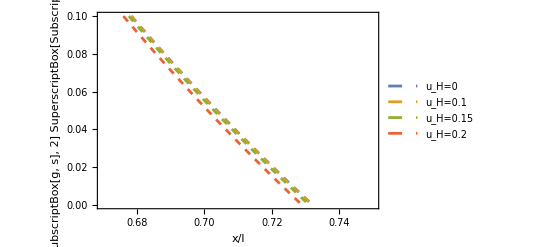

```mathematica
symmutinfplt=ListLinePlot[{symmutinf0201,symmutinf01201,symmutinf015201,symmutinf02201},PlotRange->{{0.67,0.75},{0,0.1}},Frame->True,FrameLabel->{"x/l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/R^3"Subscript[Style["Ι",FontFamily->"Times"], AB]},PlotLegends->{"u_H=0","u_H=0.1","u_H=0.15","u_H=0.2"},PlotStyle->Dashed]
```